```mathematica
files=FileNames["*.csv",NotebookDirectory[]]
```

{/Users/yaroslav/mipt/bachelor-3/semester-1/laboratory/8.1/data.csv,/Users/yaroslav/mipt/bachelor-3/semester-1/laboratory/8.1/dataerr2.csv,/Users/yaroslav/mipt/bachelor-3/semester-1/laboratory/8.1/dataerr.csv,/Users/yaroslav/mipt/bachelor-3/semester-1/laboratory/8.1/datasethi.csv}

```mathematica
importfile = files⟦2⟧
```

/Users/yaroslav/mipt/bachelor-3/semester-1/laboratory/8.1/dataerr2.csv

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
raw = Import[importfile];
raw1= Import[importfile];
```

```mathematica
raw={{"a","n"},{0,653},{10,609},{20,556},{30,525},{40,467},{50,413},{60,367},{70,331},{80,298},{90,268},{103,236}}
```

```mathematica
dataset=makeDataset[raw]
```

```mathematica
dataset1=dataset[All,<|"T"->(Around[#TexpAbs,#TexpErr]&),"W"->( Around[#WexpAbs,#WexpErr] &),"epsT"->(#epsT&)|>]
```

```mathematica
eps[T_]:=Piecewise[{{0.209, 1650≤T<1750}, {0.223, 1750≤T<1850}, {0.236, 1850≤T<1950}, {0.249, 1950≤T<2050}}]
```

```mathematica
dataset2=dataset1[6;;9,<|"T"->(#T+273&),"W"->( #W &)|>]
```

```mathematica
dataset3=dataset2[All,<|"texp"->(#T&),"sigma"->( #W/((#T)^4 eps[#T["Value"]] Around[5,0.1] 10^-4)10^8&)|>]
```

```mathematica
dataset4=dataset3[All,<|"texp"->(#T&),"sigma"->( #sigma["Value"]&)|>]
```

```mathematica
Around[dataset4[[Values]][[All,2]]//Normal]
Normal[dataset3[[Values]][[All,2]]]
```

5.210.1810^-8

{5.450.1110^-8,5.220.1110^-8,5.160.1010^-8,5.000.1010^-8}

```mathematica
{dataset2[1,"LnT"]["Value"],dataset2[1,"LnW"]["Value"]-dataset2[1,"LnepsT"]}
```

{6.82307,5.16231}

```mathematica
MantErr[a_]:=If[10≤Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10≤19,Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10,Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;2⟧],10]/10]
MantExp[a_]:=If[10≤Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10≤19,MantissaExponent[a["Uncertainty"]]⟦2⟧-2,MantissaExponent[a["Uncertainty"]]⟦2⟧-1]
DigVal[a_]:=MantissaExponent[a["Value"]]⟦2⟧-MantExp[a]+1
MantVal[a_]:=Round[FromDigits[RealDigits[a["Value"]]⟦1,;;DigVal[a]⟧],10]/10
hiTeXForm[x_]:=Which[Head[x]===Real,IntegerPart[x],-3≤MantExp[x]≤-1,ToString[Row[{PaddedForm[MantVal[x]*10.^MantExp[x],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}],"(",MantErr[x],")"}]],MantExp[x]==0,ToString[Row[{MantVal[x],"(",MantErr[x],")"}]],True,ToString[Row[{MantVal[x],"(",MantErr[x],")e",MantExp[x]}]]]
hiTeXFormVal[x_]:=Which[Head[x]===Real,IntegerPart[x],MantExp[x]≠0,ToString[PaddedForm[x["Value"],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}]],MantExp[x]==0,MantVal[x]]
hiTeXFormErr[x_]:=Which[Head[x]===Real,IntegerPart[x],MantExp[x]≠0,ToString[PaddedForm[MantErr[x]*10.^MantExp[x],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}]],MantExp[x]==0,MantErr[x]]
```

```mathematica
dataset4=dataset3[All,<|"texp"->(hiTeXForm[#texp]&),"sigmahi"->(hiTeXForm[#sigma]&)|>]
```

```mathematica
dataset4=dataset2[All,<|"TexpAbs"->(hiTeXFormVal[#T]&),"TexpErr"->(hiTeXFormErr[#T]&),"WexpAbs"->(hiTeXFormVal[#W]&),"WexpErr"->(hiTeXFormErr[#W]&)|>]
```

```mathematica
Export[NotebookDirectory[]<>"data4.csv",dataset4,"TextDelimiters"->""]
```

/Users/yaroslav/mipt/bachelor-3/semester-1/laboratory/8.1/data4.csv

```mathematica
SystemOpen["/Users/yaroslav/mipt/bachelor-3/semester-1/laboratory/8.1/dataerr.csv"]
```

```mathematica
SystemOpen["/Users/yaroslav/mipt/bachelor-3/semester-1/laboratory/8.1/dataerr.csv"]
```

```mathematica
SystemOpen["/Users/yaroslav/mipt/bachelor-3/semester-1/laboratory/8.1/datasethi.csv"]
```

```mathematica
raw={Table[n+RandomInteger[],{n,10}],Table[n,{n,10}]}
```

{{2,2,3,4,6,7,7,8,9,11},{1,2,3,4,5,6,7,8,9,10}}

FittedModel[-25.1894+3.91974 x]

-25.21.0

3.920.14

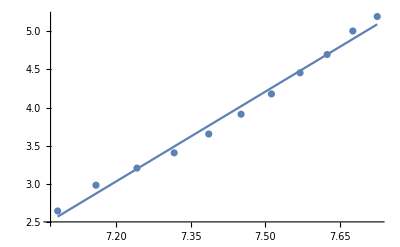

```mathematica
data=Table[{dataset2[n,"LnT"]["Value"],dataset2[n,"LnW"]["Value"]},{n,11}];
dataerr=Table[{dataset2[n,"LnT"],dataset2[n,"LnW"]},{n,11}];
fit=LinearModelFit[data,{1,x},x](*   f = a + b * x   *)
fit["ParameterTable"];
a=Around[fit["BestFitParameters"]⟦1⟧,fit["ParameterErrors"]⟦1⟧]
b=Around[fit["BestFitParameters"]⟦2⟧,fit["ParameterErrors"]⟦2⟧]
(*fit["BestFitParameters"]⟦1⟧
fit["BestFitParameters"]⟦2⟧*)
(*hiTeXForm[a]
hiTeXForm[b]*)
Show[ListPlot[dataerr],Plot[fit["BestFitParameters"]⟦1⟧+fit["BestFitParameters"]⟦2⟧x,{x,Min[data⟦All,1⟧],Max[data⟦All,1⟧]}]]
```

```mathematica
Min[data⟦All,1⟧]
Max[data⟦All,1⟧]
```

7.08322

7.72489

```mathematica
ⅇ^-25.2
```

1.13705×10^-11

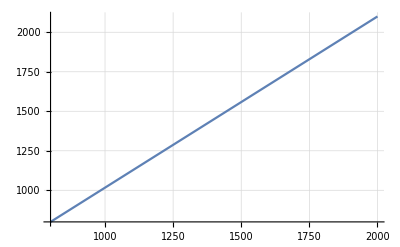

```mathematica
Plot[-66.66666666666654+1.0833333333333333x,{x,800,2000},GridLines->Automatic]
```

```mathematica
1150/41
```

1150/41

```mathematica
N[1150/41]
```

28.0488

```mathematica
hiTeXForm[Around[48,1]/Around[0.041,0.001]]
```

117(4)e1

```mathematica
Around[48,1]//hiTeXForm
```

48.0(10)

```mathematica
Around[41,1]//hiTeXForm
```

41.0(10)

```mathematica
Min[data⟦All,1⟧]
```

6.82307

```mathematica
((2 π^5(1.38 10^-16)^4)/(15 (3 10^10)^2 Around[5.21,0.18] 10^-5))^(1/3)
```

6.810.0810^-27